```mathematica
Solve[(1/kp) Tan[kp b]==(1/k) ((Tan[k b]+Tan[d])/(1-Tan[k b]+Tan[d])),Tan[d]]
```

{{Tan[d]→(-kp Tan[b k]+k Tan[b kp]-k Tan[b k] Tan[b kp])/(kp-k Tan[b kp])}}

```mathematica
fun[k_]:=(-kp Tan[b k]+k Tan[b kp]-k Tan[b k] Tan[b kp])/(kp-k Tan[b kp])
fun'[0]
```

(-b kp+Tan[b kp])/kp

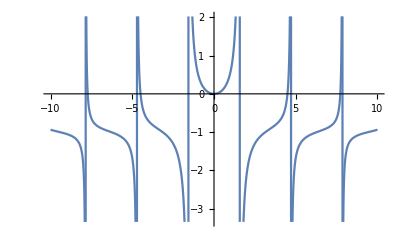

```mathematica
Plot[(-x+Tan[x])/x,{x,-10,10}]
```

```mathematica
{FindRoot[-1+Tan[x]/x==0,{x,4.49098,4.50347},WorkingPrecision->15],FindRoot[-1+Tan[x]/x==0,{x,-4.49624,-4.4846},WorkingPrecision->15]}
```

{{x→4.49340945788272},{x→-4.49340945790906}}

```mathematica
fun[k_]:=(-I kp Tan[b k]+k Tan[b I kp]-k Tan[b k] Tan[b I kp])/(kp-k Tan[b I kp])
fun'[0]
```

(-ⅈ b kp+ⅈ Tanh[b kp])/kp

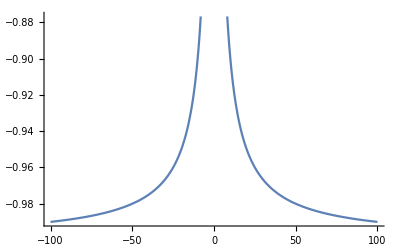

```mathematica
Plot[Re[(-ⅈ x+ⅈ Tanh[x])/x],{x,-100,100}]
Plot[Im[(-ⅈ x+ⅈ Tanh[x])/x],{x,-100,100}]
```